Problem 3

```mathematica
Clear[k,h]
h[x_]:=x+1
k[x_]:=-x^2+2
```

```mathematica
?Solve
```

Solve[expr,vars] attempts to solve the system expr of equations or inequalities for the variables vars. 
Solve[expr,vars,dom] solves over the domain dom. Common choices of dom are Reals, Integers, and Complexes.

```mathematica
Plot[{k[x],h[x]},{x,-3,3}]
```

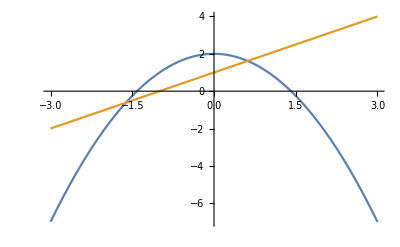

The estimated value of k(x)=h(x) is (0.6,1.6) and (-0.6,-1.6).

```mathematica
Solve[h[x]==k[x],x]
```

{{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}